```mathematica
Simulate Incomes with Dagum Distribution
```

```mathematica
universityA=Select[ExampleData[{"Statistics","UniversitySalaries"}],#[[4]]=="A"&];

salaries=Select[Table[If[universityA[[i,2]]>0,universityA[[i,3]]/universityA[[i,2]],0],{i,Length[universityA]}],#>0&];

edist=EstimatedDistribution[salaries,DagumDistribution[p,a,b]];
```

-Graphics-

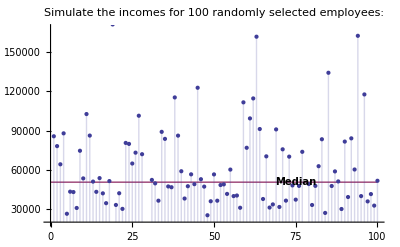

```mathematica
Show[Histogram[salaries,{0,200000,10000},"PDF",ChartStyle->"BeachColors"],Plot[PDF[TruncatedDistribution[{0,200000},edist],x],{x,0,200000},PlotStyle->Thick],BaseStyle->{FontFamily->"Verdana"},Epilog->Inset[Framed[Style[Grid[{{"Estimated distribution: "},{Round[#,.1]&/@edist}}],11],Background->LightBlue,RoundingRadius->3],{Right,Top},{Right,Top}],ImageSize->400]

ListPlot[{RandomVariate[edist,100],Tooltip[{{0,Median[edist]},{100,Median[edist]}},"Median"]},Filling->{1->Axis},Joined->{False,True},AxesOrigin->{0,20000},PlotStyle->{PointSize[Medium],Thick},BaseStyle->{FontFamily->"Verdana"},PlotLabel->"Simulate the incomes for 100 randomly selected employees:",Epilog->Inset[Style["Median",Bold,10],{75,Median[edist]},{Center,Center}],ImageSize->400]
```